# Natural gradient for multilayer linear nets

## Util

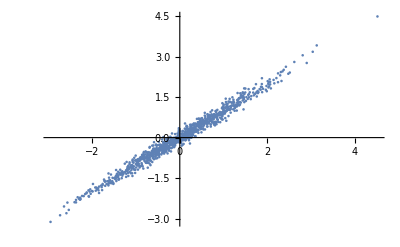

```mathematica
(* Change TensorProduct to act like Kronecker product *)
Unprotect[TensorProduct];
TensorProduct=KroneckerProduct;
Protect[TensorProduct];

On[Assert];

(* column vectorize, following Magnus, 1999 *)
vectorize[W_]:=Transpose@{Flatten@Transpose[W]};
unvectorize[Wf_, rows_]:=Transpose[Flatten/@Partition[Wf,rows]];
toscalar[v_]:=Block[{t},
t=Flatten@v;
Assert[Length[t]==1];
First@t
];

vec=vectorize;
unvec=unvectorize;

v2c[c_]:=Transpose[{c}] (* turns vector to column matrix *)
c2v[c_]:=Flatten[c] (* turns column matrix into vector *)

(* Partitions matrix into blocks {{axa,axb},{bxa,bxb}} *)
partitionMatrix[mat_,{a_,b_}]:=Module[{},
Assert[a+b==Length@mat];
Assert;[a+b==Length@matᵀ];
Internal`PartitionRagged[mat,{{a,b},{a,b}}]
];

(* Commutation matrix m,n *)
(* TODO: hide intermediate variables *)
Kmat[m_,n_]:=Module[{x},
X=Array[x,{m,n}];
before=Flatten@vectorize@X;
after=Flatten@vectorize@Transpose[X];
positions=MapIndexed[{First@#2,First@Flatten@Position[before,#]}&,after];
matrix=SparseArray[#->1&/@positions]
];

take1[x_]:=First@Flatten@x;

robustMin[x_]:=Min[Select[Flatten@x,#>1*^-10&]];

(* Symmetric square root *)
symsqrt[m_]:=Module[{U,S,W},
{U,S,W}=SingularValueDecomposition[m];
U.Sqrt[S].Transpose[W]
];


(* divide object by sum of its elements *)
normalize[x_]:=x/Total[x, 10];

(* Random uniform vector normalized to 1 *)
randomD[f_]:=Module[{temp},
temp=RandomReal[{0,1},{f}];
temp/Total[temp]
];

(* centers data where batch dimension is 1 *)
centerData[X_]:=Module[{Xc},
Xc=Mean@Transpose@X;
Transpose[#-Xc&/@Transpose[X]]
];

(* takes sizes [s1,s2,..] partitions vec into those sizes *)
listPartition[list_,sizes_]:=(
Assert[Length@list==Total@sizes, "can't partition"];
offsets={0}~Join~FoldList[Plus,sizes];
offsetPairs=Partition[offsets,2,1];
list[[#[[1]]+1;;#[[2]]]]&/@offsetPairs
);
Assert[listPartition[{1,2,3,4,5},{3,2}]=={{1,2,3},{4,5}}];

(* approximate equality testing *)
DotEqual[a_,b_]:=Norm[Flatten[{a}]-Flatten[{b}]]<1*^-10;

(* Things more specific to natural gradient stuff *)

(* partitions matrix into blocks *)
partitionMatrix2[mat_,sizes_]:=Module[{},
Internal`PartitionRagged[mat,{sizes,sizes}]
];

(* extracts i,j'th block, taking sizes from fsizes *)
matrixBlock[i_,j_,mat_]:=(
msizes=Times@@@(Partition[fs,2,1]//Rest);
partitionMatrix2[mat,msizes][[i,j]]
);

(* extracts i'th block from vector *)
vectorBlock[i_,vec_]:=(
msizes=Times@@@(Partition[fs,2,1]//Rest);
listPartition[vec,msizes][[i]]
);

magnitudeMat[i_,j_,mat_]:=Max[Abs[matrixBlock[i,j,mat]]];
magnitudeVec[i_,vec_]:=Max[Abs[vectorBlock[i,vec]]];


generateXY[e_,yvar_,extraDims_,dsize_]:=Module[{wt,mean,cov,normal,pdf,X,Xc,Y,Xa,wta,w0a,XY,n,trueCov},
SeedRandom[0];
n=2;
wt={{1,1}}; (* true relation *)
mean=0&/@Range@n;
cov={{1, 1-e},{1-e,1}};
normal=MultinormalDistribution[mean,cov];
X=RandomVariate[normal,{dsize}]//Transpose;
X=centerData[X];
Y=Dot[wt, X]+RandomVariate[NormalDistribution[0,√yvar]];
(* Add copies of first feature as redundant features *)
Xa= X~Join~Table[X[[1,All]],{i,extraDims}];
wta=Join[wt,{Table[0,{i,extraDims}]}, 2];
w0a=Join[{{1,2}},{Table[0,{i,extraDims}]}, 2];
{Xa,Y,w0a}
];
{X,Y,w0}=generateXY[0.01,1.,0,1000];
ListPlot[Transpose@X]
```

## Main

```mathematica
(* Notation:
error is Y-W[n]....W[1].W[0]=Y-W[n].....W[1].X
Wi has size f[i] x f[i-1]
Y has size f[n] x f[-1]
X has size f[0] x f[-1]
fs={f[-1],f[0],f[1],...,f[n]}
 *)


Clear[W,X,Y,y,x,fs, subW];
(* Ws gives list of matrices, Wf means flattened representation *)
(* Wf gives list of symbolic variables, W0f gives concrete values *)

On[Assert];
SeedRandom[0];
fs={10,2,2,2,1} ;
dsize=First[fs];
(* number of layers aka number of matmuls *)
n=Length[fs]-2;

dsize=First@fs;
(* makeW[0] is X *)
makeW[k_]:=Array[W[k],{fs[[k+2]],fs[[k+1]]}];
makeInitializer[k_]:=RandomReal[{0,1},{fs[[k+2]],fs[[k+1]]}];

vars=Table[makeW[k],{k,1,n}];
Ws=vars;
varsf=Flatten[vectorize/@vars];
Wf=varsf;
W0=Table[makeInitializer[k],{k,1,n}];
(* W true flat *)
Wtf={0.8062349520611257,0.8058281619635977,0.8373291816030192,0.7906864569952768,1.1965576018047888,0.30483187178626686,1.2476949293612638,0.8154112123212373,0.12928385363990855,0.8254921329944452};
(* W0 flat *)
W0f=Flatten[vectorize/@W0];
(* Y-Wn....W1.W0 *)
errEq:=Y-Fold[Dot,Reverse@vars].makeW[0];
lossEq:=take1[1/(2 dsize)errEq.errEqᵀ];

subW[Wf_]:=Thread[varsf->Wf];

X=Array[W[0],{fs[[2]],fs[[1]]}];
X0=RandomReal[{0,1},{fs[[2]],fs[[1]]}];
subX:=(
Assert[Dimensions[X0]=={fs[[2]],fs[[1]]},"X mismatch"];Thread[Flatten@X->Flatten@X0]
);

Y=Array[y,{fs[[-1]],fs[[1]]}];
Y0=RandomReal[{0,1},{fs[[-1]],fs[[1]]}];
subY:=(
Assert[Dimensions[Y0]=={Last[fs], First[fs]},"Y mismatch"];
Thread[Flatten@Y->Flatten@Y0]
);

{X0,Y0,dummy}=generateXY[0.01,1.,0,First@fs];

flatten[Ws_]:=c2v[vectorize/@Ws];
unflatten[Wf_]:=Module[{},
sizes=Rest[Times@@#&/@Partition[fs,2,1]];
flatVars=listPartition[Wf,sizes];
Table[unvectorize[flatVars[[i]],fs[[i+2]]],{i,1,Length@sizes}]
];

(* Define loss, gradient, Hessian *)
lossf[Wf_]:=(lossEq/.subW[Wf]/.subY/.subX);
loss[Ws_]:=lossf[flatten[Ws]];

Assert[vars==unflatten[varsf],"vars mismatch"];

gradEq=D[lossf[Wf],{Wf,1}];
hessEq=D[lossf[Wf],{Wf,2}];
gradf[Wf_]:=gradEq/.subW[Wf];
hessf[Wf_]:=hessEq/.subW[Wf];
ihessf[Wf_]:=PseudoInverse[hessf[Wf]];

(* Manual implementation of gradient *)

(* A[i]=W[i-1]...W[0] = fprop needed to compute derivative at layer i *)
A[Wf_,1]:=makeW[0]/.subX;
A[Wf_,i_]:=Module[{},
makeW[i-1].A[Wf,i-1]/.subW[Wf]
];

(* B[i]=W[i+1]'...err = bprop needed to compute derivative at layer i *)
err[Ws_]:=Y-A[flatten@Ws,n+1]/.subY;
B[Wf_,n]:=err[unflatten[Wf]];
B[Wf_,i_]:=Module[{},
makeW[i+1]ᵀ.B[Wf,i+1]/.subW[Wf]
];

dW[Wf_,i_]:=-B[Wf,i].A[Wf,i]ᵀ/dsize;

Assert[gradf[W0f]==flatten[dW[W0f,#]&/@Range[n]], "Gradient incorrect"]
```

## Newton Method

```mathematica
Clear[pointList,gradList,preList,lossList];
(* takes loss, grad, learning rate, produces list of losses *)
(* globals: points *)
optimizeNewton[lr_,w0f_,iters_]:=Module[{wf},
{pointList, gradList,preList, lossList}={{},{},{},{}};
wf=w0f;
For[iter=1,iter≤iters,iter++,
pointList=pointList~Append~wf;
gradList=gradList~Append~gradf[wf];
preList=preList~Append~ihessf[wf];
lossList=lossList~Append~lossf[wf];
wf=wf-lr*gradf[wf].ihessf[wf]
];
];
```

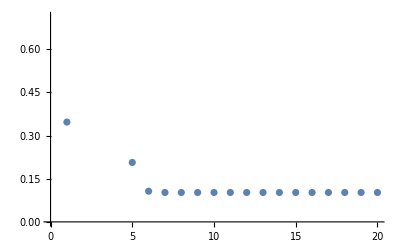

```mathematica
optimizeNewton[1.,W0f,20];
ListPlot[lossList]
```

## Natural Gradient Method

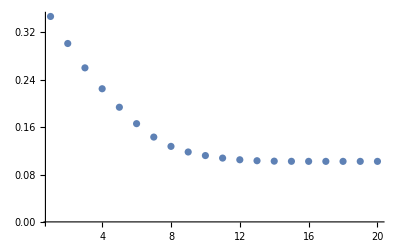

```mathematica
(* get single X *)
makeX1[i_]:=v2c[Table[W[0][j,i],{j,fs[[2]]}]];
Assert[Join@@(Table[makeX1[i],{i,10}]~Join~{2})==makeW[0]];

makeY1[i_]:=Y[[All,i]];errEq1[i_]:=makeY1[i]-Fold[Dot,Reverse@vars].makeX1[i];
lossEq1[i_]:=(take1[1/(2 dsize)errEq1[i].errEq1[i]ᵀ]);
lossf1[Wf_,i_]:=(lossEq1[i]/.subW[Wf]/.subY/.subX);
gradEq1[i_]:=D[lossf1[Wf,i],{Wf,1}];
gradf1[Wf_,i_]:=gradEq1[i]/.subW[Wf];

fisher[Wf_]:=Module[{},
(* dsize x fsize *)
gradList=Table[gradf1[Wf,i],{i,First[fs]}];
gradListᵀ.gradList/dsize
];

ifisher[Wf_]:=PseudoInverse[fisher[Wf]];

optimizeNatural[lr_,w0f_,iters_]:=Module[{wf},
{pointList, gradList,preList, lossList,temp}={{},{},{},{},{}};
wf=w0f;
For[iter=1,iter≤iters,iter++,
pointList=pointList~Append~wf;
gradList=gradList~Append~{{gradf[wf]}};
temp=temp~Append~gradf[wf];
preList=preList~Append~ihessf[wf];
lossList=lossList~Append~lossf[wf];
wf=wf-lr*gradf[wf].ifisher[wf]
];
];
optimizeNatural[.001,W0f,20];
ListPlot[lossList,PlotRange->All]
```

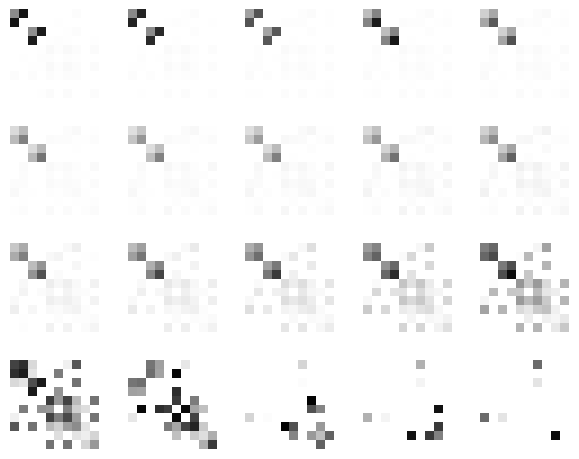

```mathematica
plots=ArrayPlot[#,PlotRange->{0,100}]&/@preList;
GraphicsGrid[Partition[plots,5]]
```

### Plot weight magnitudes in two layers

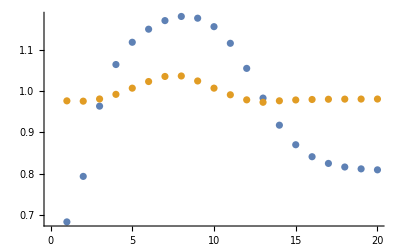

```mathematica
layer1sizes=magnitudeVec[1,#]&/@pointList;
layer2sizes=magnitudeVec[2,#]&/@pointList;
ListPlot[{layer1sizes,layer2sizes}]
```

### Plot update per layer

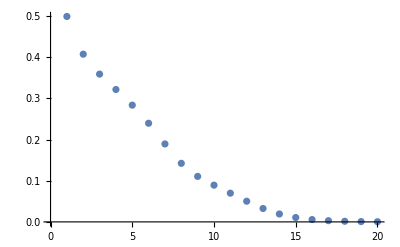

```mathematica
updates1=Table[vectorBlock[1,temp[[i]]].matrixBlock[1, 1, preList[[i]]].vectorBlock[1,temp[[i]]],{i,20}];
updates2=Table[vectorBlock[2,temp[[i]]].matrixBlock[2, 2, preList[[i]]].vectorBlock[2,temp[[i]]],{i,20}];
updates3=Table[vectorBlock[3,temp[[i]]].matrixBlock[3, 3, preList[[i]]].vectorBlock[3,temp[[i]]],{i,20}];


ListPlot[{updates1}]
```

```mathematica
ListPlot[{updates2}]
```

-Graphics-

## Regular gradient descent

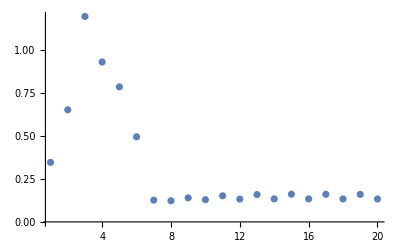

```mathematica
optimizeRegular[lr_,w0f_,iters_]:=Module[{wf},
{pointList, gradList,preList, lossList}={{},{},{},{}};
wf=w0f;
For[iter=1,iter≤iters,iter++,
pointList=pointList~Append~wf;
gradList=gradList~Append~gradf[wf];
preList=preList~Append~ihessf[wf];
lossList=lossList~Append~lossf[wf];
wf=wf-lr*gradf[wf]
];
];
optimizeRegular[.5,W0f,20];
ListPlot[lossList,PlotRange->All]
```